```mathematica
outgoing[rr_,kk_,ll_,AA_]:=(kk rr)^(-1) (kk rr) SphericalBesselJ[ll,kk rr] rr^ll;
incoming[rr_,αα_,nn_,Dfrac_]:=Exp[-αα rr^nn] (1+rr^2 Dfrac (1+3/(αα rr)+3/(αα rr)^2));
Hprime[rr_,Rconst_]:=Rconst+rr;
```

```mathematica
Subscript[k, np]^(-1./2.) ρ^2 outgoing[ρ,Subscript[k, np],1] Hprime[ρ,1] incoming[ρ,1,n,0.2]
```

(ⅇ^(-ρ^n) ρ^3 (1+ρ) (1+0.2 (1+3/ρ^2+3/ρ) ρ^2) (Sin[ρ k_np]/(ρ^2 k_np^2)-Cos[ρ k_np]/(ρ k_np)))/k_np^0.5

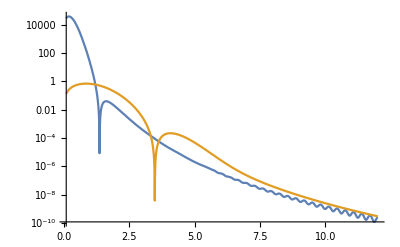

```mathematica
Tasy[kk_,nn_]:=NIntegrate[kk^(-1./2.) ρ^2 outgoing[ρ,kk,1] Hprime[ρ,0.11] incoming[ρ,1,nn,0.2],{ρ,0.01,20}]
LogPlot[{(Tasy[knp,1])^2,(Tasy[knp,2])^2},{knp,0.1,12},PlotRange->Full]
```

```mathematica
kk=1;
ll=1;
AA=2;
ff
NIntegrate[,{Subscript["ρ", 1],0.1,1,Subscript["ρ", 2],0.1,1}]
```

NIntegrate[Times@@Array[((kk ρ_##1) SphericalBesselJ[ll,kk ρ_##1] ρ_##1^ll)/(kk ρ_##1)&,{AA}],{ρ_1,0.1,1,ρ_2,0.1,1}]